```mathematica
allCrit=Map[Sort,BooleanMinimize[Reduce[
With[
{base="C",colofour="colofour"},
Fold[And,
Map[Fold[Or,Table[var>(var/.RepAtLeast[base]),{var,ListofVars[(allGraphs5[#,colofour]/.RepZero[base])]}]]&,
Select[Keys[allGraphs5],(allGraphs5[#,"atleast"]≠ (allGraphs5[#,colofour]/.RepAtLeast[base]))&]
]
]
]
]]];
```

```mathematica
tri=Table[allGraphs5[k,"colofour"],{k,alfa1s}];
```

```mathematica
allCrit2=Map[ListofVars,ExpressionToList[allCrit]];
```

```mathematica
Coeff345[list_]:=Total[Table[BaseCoeff[key,"C"],{key,(list/.RepKey["C"])}]]
```

```mathematica
DeleteColumn[mat_,n_]:=Map[Delete[#,n]&,mat]
```

```mathematica
DeleteColumn[Table[j*10,{i,10},{j,10}],10]
```

{{10,20,30,40,50,60,70,80,90},{10,20,30,40,50,60,70,80,90},{10,20,30,40,50,60,70,80,90},{10,20,30,40,50,60,70,80,90},{10,20,30,40,50,60,70,80,90},{10,20,30,40,50,60,70,80,90},{10,20,30,40,50,60,70,80,90},{10,20,30,40,50,60,70,80,90},{10,20,30,40,50,60,70,80,90},{10,20,30,40,50,60,70,80,90}}

```mathematica
mat=Map[Coeff345[ ListofVars[#]]&,Select[ExpressionToList[allCrit],Intersection[ListofVars[#],tri]=={}&]];
```

```mathematica
Select[Range[Length[mat[[1]]]],ZeroColumn[mat,#]&]
```

{}

```mathematica
ZeroColumn[mat_,n_]:=Total[Map[#[[n]]&,mat]]==0
```

```mathematica
OneColumn[mat_,n_]:=Total[Map[#[[n]]&,mat]]==Length[mat]
```

```mathematica
zeroOrOne=SetDifference[Range[52],Select[Range[Length[mat[[1]]]],ZeroColumn[mat,#]||OneColumn[mat,#]&]]
```

{2,5,6,9,11,13,16,18,19,22,24,28,31,33,35,41,45,46,47,49}

```mathematica
ZeVars=Map[Bases["C","Variables"][[#]]&,zeroOrOne]
```

{v12x3x4x5,v15x2x3x4,v1x23x4x5,v1x2x34x5,v1x2x3x45,v124x3x5,v12x35x4,v134x2x5,v135x2x4,v13x2x45,v14x23x5,v15x24x3,v1x235x4,v1x245x3,v1x25x34,v124x35,v134x25,v135x24,v13x245,v14x235}

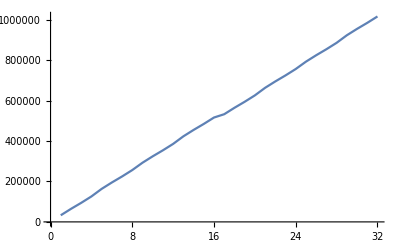

```mathematica
Map[FromDigits[#,2]&,Block[{result=mat},
Table[result=DeleteColumn[result,k],{k,Select[Range[Length[mat[[1]]]],ZeroColumn[mat,#]||OneColumn[mat,#]&]//Reverse}];
result
]//Sort]//ListLinePlot
```

```mathematica
mat7=Block[{result=mat},
Table[result=DeleteColumn[result,k],{k,Select[Range[Length[mat[[1]]]],ZeroColumn[mat,#]||OneColumn[mat,#]&]//Reverse}];
result
];
```

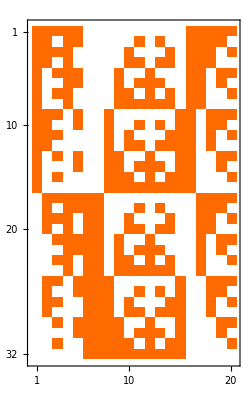

```mathematica
MatrixPlot[mat7]
```

```mathematica
EqualColumn[mat_,n_,m_]:=Fold[And,Table[mat[[k,n]]==mat[[k,m]],{k,Length[mat]}]]
```

```mathematica
Table[k->Select[Range[20],#≠k&&EqualColumn[mat7,k,#]&],{k,1,20}]
```

{1→{16},2→{18},3→{20},4→{17},5→{19},6→{7},7→{6},8→{15},9→{12},10→{14},11→{13},12→{9},13→{11},14→{10},15→{8},16→{1},17→{4},18→{2},19→{5},20→{3}}

```mathematica
Table[Labeled[ZeVars[[k]],Style[k,Red]]->With[{ll=First[Select[Range[20],#≠k&&EqualColumn[mat7,k,#]&]]},
Labeled[ZeVars[[ll]],Style[ll,Red]]],{k,1,20}]/.RepGraph["C"]
```

{-Graphics-4920701→-Graphics-51478016,-Graphics-3025302→-Graphics-36898018,-Graphics-2976703→-Graphics-31984020,-Graphics-2953304→-Graphics-38308017,-Graphics-2952505→-Graphics-36194019,-Graphics-5147506→-Graphics-4921007,-Graphics-4921007→-Graphics-5147506,-Graphics-3828108→-Graphics-29560015,-Graphics-3681709→-Graphics-30334012,-Graphics-36086010→-Graphics-29633014,-Graphics-31954011→-Graphics-29797013,-Graphics-30334012→-Graphics-3681709,-Graphics-29797013→-Graphics-31954011,-Graphics-29633014→-Graphics-36086010,-Graphics-29560015→-Graphics-3828108,-Graphics-51478016→-Graphics-4920701,-Graphics-38308017→-Graphics-2953304,-Graphics-36898018→-Graphics-3025302,-Graphics-36194019→-Graphics-2952505,-Graphics-31984020→-Graphics-2976703}

```mathematica
mat8=Block[{result=mat},
Table[result=DeleteColumn[result,k],{k,Select[Range[Length[mat[[1]]]],ZeroColumn[mat,#]&]//Reverse}];
result
];
```

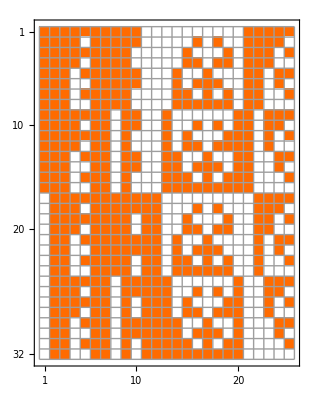

```mathematica
MatrixPlot[mat8,Mesh->All]
```

```mathematica
zero=SetDifference[Range[52],Select[Range[Length[mat[[1]]]],ZeroColumn[mat,#]&]];Length[zero]
```

25

```mathematica
ZeVars8=Map[Bases["C","Variables"][[#]]&,zero];Length[ZeVars8]
```

25

```mathematica
ZeVarxyz[k_]:=Labeled[ZeVars8[[k]],Style[k,Red]]
```

```mathematica
TableForm[Table[ZeVarxyz[k]->With[{ll=Select[Range[25],#≠k&&EqualColumn[mat8,k,#]&]},Map[ZeVarxyz,ll]
],{k,1,25}]/.RepGraph["C"]]
```

-Graphics-4920701→{-Graphics-51478021}
-Graphics-3608502→{-Graphics-3171103,-Graphics-2960506,-Graphics-2955107,-Graphics-2952709}
-Graphics-3171103→{-Graphics-3608502,-Graphics-2960506,-Graphics-2955107,-Graphics-2952709}
-Graphics-3025304→{-Graphics-36898023}
-Graphics-2976705→{-Graphics-31984025}
-Graphics-2960506→{-Graphics-3608502,-Graphics-3171103,-Graphics-2955107,-Graphics-2952709}
-Graphics-2955107→{-Graphics-3608502,-Graphics-3171103,-Graphics-2960506,-Graphics-2952709}
-Graphics-2953308→{-Graphics-38308022}
-Graphics-2952709→{-Graphics-3608502,-Graphics-3171103,-Graphics-2960506,-Graphics-2955107}
-Graphics-29525010→{-Graphics-36194024}
-Graphics-51475011→{-Graphics-49210012}
-Graphics-49210012→{-Graphics-51475011}
-Graphics-38281013→{-Graphics-29560020}
-Graphics-36817014→{-Graphics-30334017}
-Graphics-36086015→{-Graphics-29633019}
-Graphics-31954016→{-Graphics-29797018}
-Graphics-30334017→{-Graphics-36817014}
-Graphics-29797018→{-Graphics-31954016}
-Graphics-29633019→{-Graphics-36086015}
-Graphics-29560020→{-Graphics-38281013}
-Graphics-51478021→{-Graphics-4920701}
-Graphics-38308022→{-Graphics-2953308}
-Graphics-36898023→{-Graphics-3025304}
-Graphics-36194024→{-Graphics-29525010}
-Graphics-31984025→{-Graphics-2976705}

```mathematica
mat123=Transpose[ReverseSort[Transpose[Block[{result=mat},
Table[result=DeleteColumn[result,k],{k,Select[Range[Length[mat[[1]]]],ZeroColumn[mat,#]||OneColumn[mat,#]&]//Reverse}];
result
]//ReverseSort]]];
```

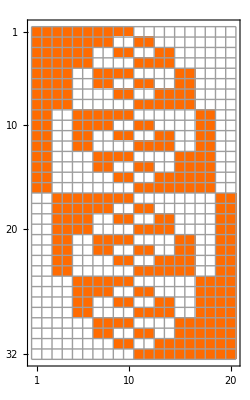

```mathematica
MatrixPlot[mat123,Mesh->All]
```

```mathematica
MatrixRank[mat123]
```

6

```mathematica
def=MatrixPlot[DeleteDuplicates[Transpose[DeleteDuplicates[Transpose[mat123]]]],Mesh->All];
```

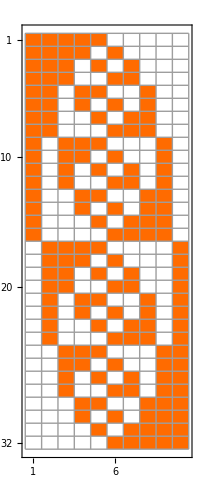

```mathematica
def
```

```mathematica
{def,Rotate[def,Pi],Rotate[def,Pi/2],Rotate[def,3Pi/2]}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
DeleteDuplicates[Transpose[DeleteDuplicates[Transpose[mat123]]]]//MatrixForm
```

(1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0
1 | 1 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0
1 | 1 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0
1 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0
1 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 0
1 | 1 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0
1 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 0
1 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 1 | 0
1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0
1 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 0
1 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0
1 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 1 | 0
1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 0
1 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0
0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 1
0 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 1
0 | 1 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 1
0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 1
0 | 1 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 1
0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1
0 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 1
0 | 1 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 1
0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 1 | 1
0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 1
0 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 1
0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 1 | 1
0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1)

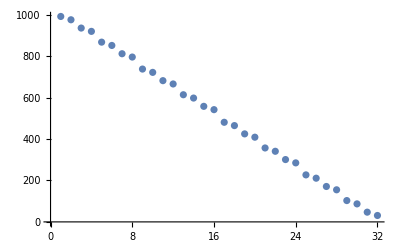

```mathematica
Map[FromDigits[#,2]&,Transpose[DeleteDuplicates[Transpose[mat123]]]]//ListPlot
```

```mathematica
Table[ZeroColumn[mat,k],{k,Length[mat]}]
```

{True,False,False,False,False,False,False,False,False,False,False,True,False,True,True,False,True,False,False,True,True,False,True,False,True,True,True,False,True,True,False,True}

```mathematica
nottri=Select[allCrit2,Intersection[#,tri]=={}&]//Flatten//DeleteDuplicates
```

{v124x35,v12x3x4x5,v134x25,v135x24,v13x245,v13x2x4x5,v14x235,v14x2x3x5,v15x2x3x4,v1x23x4x5,v1x24x3x5,v1x25x3x4,v1x2x34x5,v1x2x35x4,v1x2x3x45,v14x23x5,v1x235x4,v13x2x45,v1x245x3,v135x2x4,v15x24x3,v134x2x5,v1x25x34,v124x3x5,v12x35x4}

```mathematica
nottri//Length
```

25

```mathematica
nottri/.RepKey["C"]
```

{51478,49207,38308,36898,36194,36085,31984,31711,30253,29767,29605,29551,29533,29527,29525,31954,29797,36086,29633,36817,30334,38281,29560,51475,49210}

```mathematica
Table[allGraphs5[k,"comp"]=Greater;allGraphs5[k,"compwhy"]="Ad absurdum avoid tri";allGraphs5[k,"atleast"]=Max[1,allGraphs5[k,"atleast"]];
allGraphs5[k,"atleastwhy"]="omdat het kan";,{k,(nottri/.RepKey["C"])}]
```

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
PropagateAtLeast[]
```

{1795,{29520,29523,29521,29529,29514,29515,29517,29512,29513,29542,29493,29496,29497,29494,29502,29506,29487,29488,29485,29574,29602,29577,29430,29439,29442,29443,29446,29440,29433,29434,29436,29431,29460,29469,29412,29412,29415,29416,29417,29413,29406,29407,29404,29405,29766,29737,29676,29677,29706,29647,29241,29268,29277,29280,29281,29282,29278,29271,29272,29269,29270,29296,29305,29250,29250,29253,29254,29257,29251,29244,29245,29247,29242,29322,29350,29353,29378,29325,29187,29196,29199,29200,29197,29205,29209,29190,29191,29188,29214,29223,29232,29169,29169,29172,29173,29174,29176,29170,29178,29182,29163,29164,29166,29161,29162,30244,30172,30001,30010,30082,29929,28674,28755,28782,28791,28794,28795,28792,28800,28804,28785,28786,28783,28764,28767,28768,28765,28773,28777,28758,28759,28756,28845,28873,28876,28848,28701,28701,28710,28713,28714,28711,28704,28704,28705,28705,28702,28702,28683,28686,28687,28684,28677,28677,28678,28678,28675,28675,29037,29038,29008,28947,28948,28918,28512,28539,28548,28551,28552,28549,28542,28543,28540,28521,28524,28525,28522,28515,28516,28513,28593,28621,28624,28596,28458,28458,28467,28470,28471,28468,28476,28480,28461,28461,28462,28462,28459,28459,28440,28443,28444,28441,28449,28453,28434,28434,28435,28435,28432,28432,31708,31684,31924,31465,31468,31492,31441,31444,30978,30981,30954,31194,31224,30735,30738,30711,26973,27216,27297,27324,27333,27336,27337,27340,27334,27327,27328,27330,27325,27355,27364,27306,27309,27310,27307,27300,27301,27298,27243,27252,27255,27256,27253,27246,27247,27244,27273,27282,27225,27228,27229,27226,27219,27220,27217,27459,27549,27579,27580,27610,27550,27489,27490,27519,27460,27054,27054,27081,27090,27093,27094,27091,27084,27085,27082,27109,27118,27063,27063,27066,27067,27070,27064,27064,27057,27058,27060,27055,27055,27000,27009,27012,27013,27010,27003,27004,27001,27027,27036,26982,26982,26985,26986,26989,26983,26983,26976,26977,26979,26974,26974,28056,28065,27984,27813,27822,27741,26487,26568,26568,26595,26604,26607,26608,26609,26605,26598,26599,26596,26597,26577,26580,26581,26578,26571,26572,26569,26514,26523,26526,26527,26524,26517,26518,26515,26496,26499,26500,26501,26497,26490,26491,26488,26489,26730,26820,26850,26851,26821,26760,26761,26731,26325,26325,26352,26361,26364,26365,26366,26362,26355,26356,26353,26354,26334,26334,26337,26338,26335,26335,26328,26329,26326,26326,26271,26280,26283,26284,26281,26274,26275,26272,26253,26253,26256,26257,26258,26254,26254,26247,26248,26245,26245,26246,36057,36084,36058,36138,36003,36004,36030,35978,36736,35325,35352,35353,35326,35406,35434,35271,35272,35245,38254,37548,33780,33861,33888,33889,33916,33862,33807,33808,33834,33781,34539,34620,33129,33129,33156,33157,33158,33130,33075,33076,33049,33050,21870,22599,22842,22923,22950,22959,22962,22963,22964,22960,22953,22954,22951,22952,22981,22990,22932,22932,22935,22935,22936,22933,22926,22926,22927,22924,23044,23072,23016,22869,22878,22881,22882,22879,22872,22873,22870,22899,22908,22851,22851,22854,22854,22855,22856,22852,22845,22845,22846,22843,22844,22680,22707,22716,22719,22720,22721,22717,22710,22711,22708,22709,22735,22744,22689,22689,22692,22692,22693,22690,22683,22683,22684,22681,22792,22817,22764,22626,22635,22638,22639,22636,22629,22630,22627,22653,22662,22608,22608,22611,22611,22612,22613,22609,22602,22602,22603,22600,22601,23356,23599,23680,23689,23770,23608,23437,23446,23518,23365,22113,22113,22194,22221,22230,22233,22234,22237,22231,22224,22225,22227,22222,22203,22203,22206,22206,22207,22204,22197,22197,22198,22195,22284,22312,22315,22318,22287,22140,22149,22152,22153,22156,22150,22143,22144,22146,22141,22122,22122,22125,22125,22126,22123,22116,22116,22117,22114,21951,21951,21978,21987,21990,21991,21988,21981,21982,21979,21960,21960,21963,21963,21964,21967,21961,21954,21954,21955,21957,21952,22032,22060,22063,22035,22038,21897,21906,21909,21910,21907,21900,21901,21898,21879,21879,21882,21882,21883,21886,21880,21873,21873,21874,21876,21871,24138,24868,25111,25138,25141,25168,25114,24895,24898,24922,24871,24381,24408,24411,24384,24165,24168,24141,24144,20412,20655,20736,20736,20763,20772,20775,20776,20773,20781,20785,20766,20767,20764,20794,20812,20745,20745,20748,20748,20749,20746,20754,20758,20739,20739,20740,20737,20682,20691,20694,20695,20692,20685,20686,20683,20712,20721,20664,20664,20667,20667,20668,20665,20658,20658,20659,20656,20493,20493,20520,20529,20532,20533,20530,20523,20524,20521,20548,20557,20502,20502,20505,20505,20506,20503,20496,20496,20497,20494,20439,20448,20451,20452,20449,20457,20461,20442,20443,20440,20466,20475,20484,20421,20421,20424,20424,20425,20422,20430,20434,20415,20415,20416,20413,21168,21411,21492,21501,21420,21249,21258,21177,19926,19926,20007,20007,20034,20043,20046,20047,20048,20050,20044,20052,20056,20037,20038,20040,20035,20036,20016,20016,20019,20019,20020,20017,20025,20025,20029,20010,20010,20011,20008,19953,19962,19965,19966,19969,19963,19956,19957,19959,19954,19935,19935,19938,19938,19939,19940,19936,19929,19929,19930,19927,19928,19764,19764,19791,19800,19803,19804,19805,19801,19794,19795,19792,19793,19773,19773,19776,19776,19777,19780,19774,19767,19767,19768,19770,19765,19710,19719,19722,19723,19720,19728,19732,19713,19714,19711,19692,19692,19692,19695,19695,19696,19697,19699,19693,19701,19701,19705,19686,19686,19687,19689,19684,19685,49206,49204,49197,49198,49200,49195,48450,48451,48448,48441,48442,48439,51472,50718,46926,46935,46938,46939,46942,46936,46929,46930,46932,46927,46179,46182,46183,46180,46173,46174,46171,42402,42403,42400,42393,42394,42391,41646,41647,41650,41644,41637,41638,41640,41635,44659,44662,43905,43908,40122,40131,40134,40135,40132,40125,40126,40123,39375,39378,39379,39382,39376,39369,39370,39372,39367,6561,9801,9837,9840,9841,9842,9844,9838,9846,9850,9831,9832,9834,9829,9830,9810,9813,9814,9811,9819,9823,9804,9805,9802,9747,9756,9759,9760,9763,9757,9750,9751,9753,9748,9729,9732,9733,9734,9730,9723,9724,9721,9722,9558,9585,9594,9597,9598,9599,9595,9588,9589,9586,9587,9567,9570,9571,9574,9568,9561,9562,9564,9559,9504,9513,9516,9517,9514,9522,9526,9507,9508,9505,9486,9489,9490,9491,9493,9487,9495,9499,9480,9481,9483,9478,9479,10534,10543,10462,10291,10300,10219,8991,9072,9072,9099,9108,9111,9112,9109,9117,9121,9102,9103,9100,9130,9139,9148,9081,9084,9085,9082,9090,9094,9075,9076,9073,9018,9027,9030,9031,9028,9021,9022,9019,9048,9057,9000,9003,9004,9001,8994,8995,8992,8829,8856,8865,8868,8869,8866,8859,8860,8857,8884,8893,8838,8841,8842,8839,8832,8833,8830,8775,8784,8787,8788,8785,8793,8797,8778,8779,8776,8802,8811,8820,8757,8760,8761,8758,8766,8770,8751,8752,8749,10944,11674,11917,11944,11947,11950,11920,11701,11704,11677,11680,11187,11214,11217,11190,10971,10974,10998,10947,7290,7533,7614,7641,7650,7653,7654,7657,7651,7644,7645,7647,7642,7623,7626,7627,7624,7617,7618,7615,7704,7732,7735,7738,7707,7560,7569,7572,7573,7576,7570,7563,7564,7566,7561,7542,7545,7546,7543,7536,7537,7534,7371,7398,7407,7410,7411,7408,7401,7402,7399,7380,7383,7384,7387,7381,7374,7375,7377,7372,7452,7480,7483,7455,7458,7317,7326,7329,7330,7327,7320,7321,7318,7299,7302,7303,7306,7300,7293,7294,7296,7291,8346,8355,8436,8274,8103,8112,8184,8031,6804,6804,6885,6912,6921,6924,6925,6926,6922,6915,6916,6913,6914,6943,6952,6894,6897,6898,6895,6888,6889,6886,6975,6975,7003,7006,7034,6978,6831,6840,6843,6844,6841,6834,6835,6832,6861,6870,6813,6816,6817,6818,6814,6807,6808,6805,6806,6642,6669,6678,6681,6682,6683,6679,6672,6673,6670,6671,6697,6706,6651,6654,6655,6652,6645,6646,6643,6723,6723,6751,6754,6779,6726,6588,6597,6600,6601,6598,6591,6592,6589,6615,6624,6570,6573,6574,6575,6571,6564,6565,6562,6563,16131,16158,16159,16160,16132,16077,16078,16052,16783,16864,15399,15426,15427,15400,15345,15346,15372,15319,18247,18274,17541,17568,13854,13935,13962,13963,13936,14016,13881,13882,13855,14586,14667,14748,13203,13230,13231,13232,13258,13204,13284,13312,13340,13149,13150,13176,13123,13124,2187,2916,3159,3240,3267,3276,3279,3280,3281,3277,3270,3271,3268,3269,3249,3252,3253,3250,3243,3244,3241,3186,3195,3198,3199,3196,3189,3190,3187,3168,3171,3172,3173,3169,3162,3163,3160,3161,3522,3523,3493,3432,3433,3403,2997,3024,3033,3036,3037,3038,3034,3027,3028,3025,3026,3006,3009,3010,3007,3000,3001,2998,2943,2952,2955,2956,2953,2946,2947,2944,2925,2928,2929,2930,2926,2919,2920,2917,2918,3646,3889,3970,3979,3898,3727,3736,3655,2430,2511,2538,2547,2550,2551,2554,2548,2541,2542,2544,2539,2569,2578,2520,2523,2524,2521,2514,2515,2512,2457,2466,2469,2470,2473,2467,2460,2461,2463,2458,2487,2496,2439,2442,2443,2440,2433,2434,2431,2793,2794,2824,2764,2703,2704,2733,2674,2268,2295,2304,2307,2308,2305,2298,2299,2296,2323,2332,2277,2280,2281,2284,2278,2271,2272,2274,2269,2214,2223,2226,2227,2224,2217,2218,2215,2241,2250,2196,2199,2200,2203,2197,2190,2191,2193,2188,4374,5104,5347,5374,5377,5350,5590,5620,5131,5134,5107,4617,4617,4644,4647,4650,4674,4620,4860,4890,4920,4401,4404,4428,4377,4380,729,972,1053,1080,1089,1092,1093,1090,1098,1102,1083,1084,1081,1062,1065,1066,1063,1071,1075,1056,1057,1054,1143,1171,1174,1146,999,1008,1011,1012,1009,1002,1003,1000,981,984,985,982,975,976,973,1215,1305,1335,1336,1306,1245,1246,1216,810,837,846,849,850,847,840,841,838,819,822,823,820,813,814,811,891,919,922,894,756,765,768,769,766,774,778,759,760,757,738,741,742,739,747,751,732,733,730,1458,1701,1782,1791,1872,1710,1539,1548,1620,1467,243,243,324,351,360,363,364,365,367,361,369,373,354,355,357,352,353,382,400,333,336,337,334,342,346,327,328,325,414,414,442,445,448,473,417,270,279,282,283,286,280,273,274,276,271,300,309,252,255,256,257,253,246,247,244,245,486,576,606,607,637,577,516,517,546,487,81,108,117,120,121,122,118,111,112,109,110,136,145,90,93,94,97,91,84,85,87,82,162,162,190,193,218,165,168,27,36,39,40,37,45,49,30,31,28,54,63,72,9,12,13,14,16,10,18,22,3,4,6,1,2}}

```mathematica
PropagateComp[]
```

PropagateComp[]

```mathematica
Table[allGraphs5[k,"comp"],{k,Keys[allGraphs5]}]//Tally//Sort
```

{{Equal,1},{Greater,1719},{GreaterEqual,175}}

```mathematica
allCrit2=BooleanMinimize[Reduce[
With[
{base="C",colofour="colofour"},
Fold[And,
Map[Fold[Or,Table[var>(var/.RepAtLeast[base]),{var,ListofVars[(allGraphs5[#,colofour]/.RepZero[base])]}]]&,
Select[Keys[allGraphs5],(allGraphs5[#,"atleast"]≠ (allGraphs5[#,colofour]/.RepAtLeast[base]))&]
]
]
]
]]
```

v124x35>0&&v124x3x5>0&&v12x35x4>0&&v12x3x4x5>0&&v134x25>0&&v134x2x5>0&&v135x24>0&&v135x2x4>0&&v13x245>0&&v13x2x45>0&&v13x2x4x5>0&&v14x235>0&&v14x23x5>0&&v14x2x3x5>0&&v15x24x3>0&&v15x2x3x4>0&&v1x235x4>0&&v1x23x4x5>0&&v1x245x3>0&&v1x24x3x5>0&&v1x25x34>0&&v1x25x3x4>0&&v1x2x34x5>0&&v1x2x35x4>0&&v1x2x3x45>0

```mathematica
Length[allCrit2]
```

25

```mathematica
allCrit2/.RepGraph["C"]
```

-Graphics-514780>0&&-Graphics-514750>0&&-Graphics-492100>0&&-Graphics-492070>0&&-Graphics-383080>0&&-Graphics-382810>0&&-Graphics-368980>0&&-Graphics-368170>0&&-Graphics-361940>0&&-Graphics-360860>0&&-Graphics-360850>0&&-Graphics-319840>0&&-Graphics-319540>0&&-Graphics-317110>0&&-Graphics-303340>0&&-Graphics-302530>0&&-Graphics-297970>0&&-Graphics-297670>0&&-Graphics-296330>0&&-Graphics-296050>0&&-Graphics-295600>0&&-Graphics-295510>0&&-Graphics-295330>0&&-Graphics-295270>0&&-Graphics-295250>0

```mathematica
allCrit2=With[
{base="C",colofour="colofour"},
Fold[And,
Map[Fold[Or,Table[var>(var/.RepAtLeast[base]),{var,ListofVars[(allGraphs5[#,colofour]/.RepZero[base])]}]]&,
Select[Keys[allGraphs5],(allGraphs5[#,"atleast"]≠ (allGraphs5[#,colofour]/.RepAtLeast[base]))&]
]
]
]//Reduce//BooleanMinimize
```

v124x35>0&&v124x3x5>0&&v12x35x4>0&&v12x3x4x5>0&&v134x25>0&&v134x2x5>0&&v135x24>0&&v135x2x4>0&&v13x245>0&&v13x2x45>0&&v13x2x4x5>0&&v14x235>0&&v14x23x5>0&&v14x2x3x5>0&&v15x24x3>0&&v15x2x3x4>0&&v1x235x4>0&&v1x23x4x5>0&&v1x245x3>0&&v1x24x3x5>0&&v1x25x34>0&&v1x25x3x4>0&&v1x2x34x5>0&&v1x2x35x4>0&&v1x2x3x45>0

```mathematica
With[
{base="C",colofour="colofour"},
Select[Keys[allGraphs5],(allGraphs5[#,"atleast"]≠ (allGraphs5[#,colofour]/.RepAtLeast[base]))&]
]
```

{0,19683,26244,28431,29160,29403,29484,29520,29523,29525,29527,29521,29529,29533,29514,29515,29517,29512,29513,29542,29551,29560,29493,29496,29497,29494,29502,29506,29487,29488,29485,29574,29602,29605,29633,29577,29430,29439,29442,29443,29446,29440,29433,29434,29436,29431,29460,29469,29412,29415,29416,29417,29413,29406,29407,29404,29405,29646,29736,29766,29767,29797,29737,29676,29677,29706,29647,29241,29268,29277,29280,29281,29282,29278,29271,29272,29269,29270,29296,29305,29250,29253,29254,29257,29251,29244,29245,29247,29242,29322,29350,29353,29378,29325,29187,29196,29199,29200,29197,29205,29209,29190,29191,29188,29214,29223,29232,29169,29172,29173,29174,29176,29170,29178,29182,29163,29164,29166,29161,29162,29920,30163,30244,30253,30334,30172,30001,30010,30082,29929,28674,28755,28782,28791,28794,28795,28792,28800,28804,28785,28786,28783,28764,28767,28768,28765,28773,28777,28758,28759,28756,28845,28873,28876,28848,28701,28710,28713,28714,28711,28704,28705,28702,28683,28686,28687,28684,28677,28678,28675,28917,29007,29037,29038,29008,28947,28948,28918,28512,28539,28548,28551,28552,28549,28542,28543,28540,28521,28524,28525,28522,28515,28516,28513,28593,28621,28624,28596,28458,28467,28470,28471,28468,28476,28480,28461,28462,28459,28440,28443,28444,28441,28449,28453,28434,28435,28432,30708,31438,31681,31708,31711,31684,31924,31954,31984,31465,31468,31492,31441,31444,30951,30978,30981,30954,31194,31224,30735,30738,30711,26973,27216,27297,27324,27333,27336,27337,27340,27334,27327,27328,27330,27325,27355,27364,27306,27309,27310,27307,27300,27301,27298,27243,27252,27255,27256,27259,27253,27246,27247,27249,27244,27273,27282,27225,27228,27229,27226,27219,27220,27217,27459,27549,27579,27580,27610,27550,27489,27490,27519,27460,27054,27081,27090,27093,27094,27091,27084,27085,27082,27109,27118,27063,27066,27067,27070,27064,27057,27058,27060,27055,27000,27009,27012,27013,27010,27003,27004,27001,27027,27036,26982,26985,26986,26989,26983,26976,26977,26979,26974,27732,27975,28056,28065,27984,27813,27822,27741,26487,26568,26595,26604,26607,26608,26609,26605,26598,26599,26596,26597,26577,26580,26581,26578,26571,26572,26569,26514,26523,26526,26527,26524,26517,26518,26515,26496,26499,26500,26501,26497,26490,26491,26488,26489,26730,26820,26850,26851,26821,26760,26761,26731,26325,26352,26361,26364,26365,26366,26362,26355,26356,26353,26354,26334,26337,26338,26335,26328,26329,26326,26271,26280,26283,26284,26281,26274,26275,26272,26253,26256,26257,26258,26254,26247,26248,26245,26246,33048,35244,35976,36057,36084,36085,36086,36058,36138,36194,36003,36004,36030,35977,35978,36736,36817,36898,35325,35352,35353,35326,35406,35434,35271,35272,35245,37521,38254,38281,38308,37548,33780,33861,33888,33889,33916,33862,33807,33808,33834,33781,34539,34620,33129,33156,33157,33158,33130,33075,33076,33049,33050,21870,22599,22842,22923,22950,22959,22962,22963,22964,22960,22953,22954,22951,22952,22981,22990,22932,22935,22936,22933,22926,22927,22924,23013,23041,23044,23072,23016,22869,22878,22881,22882,22879,22872,22873,22870,22899,22908,22851,22854,22855,22856,22852,22845,22846,22843,22844,22680,22707,22716,22719,22720,22721,22717,22710,22711,22708,22709,22735,22744,22689,22692,22693,22690,22683,22684,22681,22761,22789,22792,22817,22764,22626,22635,22638,22639,22636,22629,22630,22627,22653,22662,22608,22611,22612,22613,22609,22602,22603,22600,22601,23356,23599,23680,23689,23770,23608,23437,23446,23518,23365,22113,22194,22221,22230,22233,22234,22237,22231,22224,22225,22227,22222,22203,22206,22207,22204,22197,22198,22195,22284,22312,22315,22318,22287,22140,22149,22152,22153,22156,22150,22143,22144,22146,22141,22122,22125,22126,22123,22116,22117,22114,21951,21978,21987,21990,21991,21988,21981,21982,21979,21960,21963,21964,21967,21961,21954,21955,21957,21952,22032,22060,22063,22035,22038,21897,21906,21909,21910,21907,21900,21901,21898,21879,21882,21883,21886,21880,21873,21874,21876,21871,24138,24868,25111,25138,25141,25168,25114,24895,24898,24922,24871,24381,24408,24411,24384,24165,24168,24141,24144,20412,20655,20736,20763,20772,20775,20776,20773,20781,20785,20766,20767,20764,20794,20803,20812,20745,20748,20749,20746,20754,20758,20739,20740,20737,20682,20691,20694,20695,20692,20685,20686,20683,20712,20721,20664,20667,20668,20665,20658,20659,20656,20493,20520,20529,20532,20533,20530,20523,20524,20521,20548,20557,20502,20505,20506,20503,20496,20497,20494,20439,20448,20451,20452,20449,20457,20461,20442,20443,20440,20466,20475,20484,20421,20424,20425,20422,20430,20434,20415,20416,20413,21168,21411,21492,21501,21420,21249,21258,21177,19926,20007,20034,20043,20046,20047,20048,20050,20044,20052,20056,20037,20038,20040,20035,20036,20016,20019,20020,20017,20025,20029,20010,20011,20008,19953,19962,19965,19966,19969,19963,19956,19957,19959,19954,19935,19938,19939,19940,19936,19929,19930,19927,19928,19764,19791,19800,19803,19804,19805,19801,19794,19795,19792,19793,19773,19776,19777,19780,19774,19767,19768,19770,19765,19710,19719,19722,19723,19720,19728,19732,19713,19714,19711,19692,19695,19696,19697,19699,19693,19701,19705,19686,19687,19689,19684,19685,39366,46170,48438,49194,49203,49206,49207,49210,49204,49197,49198,49200,49195,48447,48450,48451,48448,48441,48442,48439,50715,51472,51475,51478,50718,46926,46935,46938,46939,46942,46936,46929,46930,46932,46927,46179,46182,46183,46180,46173,46174,46171,41634,42390,42399,42402,42403,42400,42393,42394,42391,41643,41646,41647,41650,41644,41637,41638,41640,41635,43902,44659,44662,43905,43908,40122,40131,40134,40135,40132,40125,40126,40123,39375,39378,39379,39382,39376,39369,39370,39372,39367,6561,8748,9477,9720,9801,9828,9837,9840,9841,9842,9844,9838,9846,9850,9831,9832,9834,9829,9830,9810,9813,9814,9811,9819,9823,9804,9805,9802,9747,9756,9759,9760,9763,9757,9750,9751,9753,9748,9729,9732,9733,9734,9730,9723,9724,9721,9722,9558,9585,9594,9597,9598,9599,9595,9588,9589,9586,9587,9567,9570,9571,9574,9568,9561,9562,9564,9559,9504,9513,9516,9517,9514,9522,9526,9507,9508,9505,9486,9489,9490,9491,9493,9487,9495,9499,9480,9481,9483,9478,9479,10210,10453,10534,10543,10462,10291,10300,10219,8991,9072,9099,9108,9111,9112,9109,9117,9121,9102,9103,9100,9130,9139,9148,9081,9084,9085,9082,9090,9094,9075,9076,9073,9018,9027,9030,9031,9028,9021,9022,9019,9048,9057,9000,9003,9004,9001,8994,8995,8992,8829,8856,8865,8868,8869,8866,8859,8860,8857,8884,8893,8838,8841,8842,8839,8832,8833,8830,8775,8784,8787,8788,8785,8793,8797,8778,8779,8776,8802,8811,8820,8757,8760,8761,8758,8766,8770,8751,8752,8749,10944,11674,11917,11944,11947,11950,11920,11701,11704,11677,11680,11187,11214,11217,11190,10971,10974,10998,10947,7290,7533,7614,7641,7650,7653,7654,7657,7651,7644,7645,7647,7642,7623,7626,7627,7624,7617,7618,7615,7704,7732,7735,7738,7707,7560,7569,7572,7573,7576,7570,7563,7564,7566,7561,7542,7545,7546,7543,7536,7537,7534,7371,7398,7407,7410,7411,7408,7401,7402,7399,7380,7383,7384,7387,7381,7374,7375,7377,7372,7452,7480,7483,7455,7458,7317,7326,7329,7330,7327,7320,7321,7318,7299,7302,7303,7306,7300,7293,7294,7296,7291,8022,8265,8346,8355,8436,8274,8103,8112,8184,8031,6804,6885,6912,6921,6924,6925,6926,6922,6915,6916,6913,6914,6943,6952,6894,6897,6898,6895,6888,6889,6886,6975,7003,7006,7034,6978,6831,6840,6843,6844,6841,6834,6835,6832,6861,6870,6813,6816,6817,6818,6814,6807,6808,6805,6806,6642,6669,6678,6681,6682,6683,6679,6672,6673,6670,6671,6697,6706,6651,6654,6655,6652,6645,6646,6643,6723,6751,6754,6779,6726,6588,6597,6600,6601,6598,6591,6592,6589,6615,6624,6570,6573,6574,6575,6571,6564,6565,6562,6563,13122,15318,16050,16131,16158,16159,16160,16132,16077,16078,16051,16052,16783,16864,15399,15426,15427,15400,15345,15346,15372,15319,17514,18247,18274,17541,17568,13854,13935,13962,13963,13936,14016,13881,13882,13855,14586,14667,14748,13203,13230,13231,13232,13258,13204,13284,13312,13340,13149,13150,13176,13123,13124,2187,2916,3159,3240,3267,3276,3279,3280,3281,3277,3270,3271,3268,3269,3249,3252,3253,3250,3243,3244,3241,3186,3195,3198,3199,3196,3189,3190,3187,3168,3171,3172,3173,3169,3162,3163,3160,3161,3402,3492,3522,3523,3493,3432,3433,3403,2997,3024,3033,3036,3037,3038,3034,3027,3028,3025,3026,3006,3009,3010,3007,3000,3001,2998,2943,2952,2955,2956,2953,2946,2947,2944,2925,2928,2929,2930,2926,2919,2920,2917,2918,3646,3889,3970,3979,3898,3727,3736,3655,2430,2511,2538,2547,2550,2551,2554,2548,2541,2542,2544,2539,2569,2578,2520,2523,2524,2521,2514,2515,2512,2457,2466,2469,2470,2473,2467,2460,2461,2463,2458,2487,2496,2439,2442,2443,2440,2433,2434,2431,2673,2763,2793,2794,2824,2764,2703,2704,2733,2674,2268,2295,2304,2307,2308,2305,2298,2299,2296,2323,2332,2277,2280,2281,2284,2278,2271,2272,2274,2269,2214,2223,2226,2227,2224,2217,2218,2215,2241,2250,2196,2199,2200,2203,2197,2190,2191,2193,2188,4374,5104,5347,5374,5377,5350,5590,5620,5131,5134,5107,4617,4644,4647,4650,4674,4620,4860,4890,4920,4401,4404,4428,4377,4380,729,972,1053,1080,1089,1092,1093,1090,1098,1102,1083,1084,1081,1062,1065,1066,1063,1071,1075,1056,1057,1054,1143,1171,1174,1146,999,1008,1011,1012,1009,1002,1003,1000,981,984,985,982,975,976,973,1215,1305,1335,1336,1306,1245,1246,1216,810,837,846,849,850,847,840,841,838,819,822,823,820,813,814,811,891,919,922,894,756,765,768,769,766,774,778,759,760,757,738,741,742,739,747,751,732,733,730,1458,1701,1782,1791,1872,1710,1539,1548,1620,1467,243,324,351,360,363,364,365,367,361,369,373,354,355,357,352,353,382,391,400,333,336,337,334,342,346,327,328,325,414,442,445,448,473,417,270,279,282,283,286,280,273,274,276,271,300,309,252,255,256,257,253,246,247,244,245,486,576,606,607,637,577,516,517,546,487,81,108,117,120,121,122,118,111,112,109,110,136,145,90,93,94,97,91,84,85,87,82,162,190,193,218,165,168,27,36,39,40,37,45,49,30,31,28,54,63,72,9,12,13,14,16,10,18,22,3,4,6,1,2}

```mathematica
Reduce[With[
{base="C",colofour="colofour"},
Fold[And,
Map[Fold[Or,Table[var>(var/.RepAtLeast[base]),{var,ListofVars[(allGraphs5[#,colofour]/.RepZero[base])]}]]&,
Select[Keys[allGraphs5],(allGraphs5[#,"atleast"]≠ (allGraphs5[#,colofour]/.RepAtLeast[base]))&]
]
]
],v12x3x45]
```

v14x23x5>0&&v14x2x3x5>0&&v14x235>0&&v15x24x3>0&&v13x2x4x5>0&&v15x2x3x4>0&&v13x2x45>0&&v1x235x4>0&&v13x245>0&&v1x23x4x5>0&&v135x2x4>0&&v1x245x3>0&&v135x24>0&&v1x24x3x5>0&&v134x2x5>0&&v1x25x34>0&&v134x25>0&&v1x25x3x4>0&&v12x3x4x5>0&&v1x2x34x5>0&&v12x35x4>0&&v1x2x35x4>0&&v124x3x5>0&&v1x2x3x45>0&&v124x35>0

```mathematica
Table[GreaterEqual[allGraphs5[k,"colofour"],allGraphs5[k,"atleast"]]
,{k,allGraphs5AtomKeys}]
```

{v1x2x3x4x5≥0,v1x2x3x45≥1,v1x2x35x4≥1,v1x2x34x5≥1,v1x2x345≥1,v1x25x3x4≥1,v1x25x34≥1,v1x24x3x5≥1,v1x24x35≥0,v1x245x3≥1,v1x23x4x5≥1,v1x23x45≥1,v1x235x4≥1,v1x234x5≥1,v1x2345≥1,v15x2x3x4≥1,v15x2x34≥1,v15x24x3≥1,v15x23x4≥1,v15x234≥1,v14x2x3x5≥1,v14x2x35≥0,v14x25x3≥0,v14x23x5≥1,v14x235≥1,v145x2x3≥1,v145x23≥1,v13x2x4x5≥1,v13x2x45≥1,v13x25x4≥0,v13x24x5≥0,v13x245≥1,v135x2x4≥1,v135x24≥1,v134x2x5≥1,v134x25≥1,v1345x2≥1,v12x3x4x5≥1,v12x3x45≥1,v12x35x4≥1,v12x34x5≥1,v12x345≥1,v125x3x4≥1,v125x34≥1,v124x3x5≥1,v124x35≥1,v1245x3≥1,v123x4x5≥1,v123x45≥1,v1235x4≥1,v1234x5≥1,v12345≥1}

```mathematica
Fold[And,
Table[GreaterEqual[allGraphs5[k,"colofour"],allGraphs5[k,"atleast"]]
,{k,allGraphs5AtomKeys}]]
```

v1x2x3x4x5≥0&&v1x2x3x45≥1&&v1x2x35x4≥1&&v1x2x34x5≥1&&v1x2x345≥1&&v1x25x3x4≥1&&v1x25x34≥1&&v1x24x3x5≥1&&v1x24x35≥0&&v1x245x3≥1&&v1x23x4x5≥1&&v1x23x45≥1&&v1x235x4≥1&&v1x234x5≥1&&v1x2345≥1&&v15x2x3x4≥1&&v15x2x34≥1&&v15x24x3≥1&&v15x23x4≥1&&v15x234≥1&&v14x2x3x5≥1&&v14x2x35≥0&&v14x25x3≥0&&v14x23x5≥1&&v14x235≥1&&v145x2x3≥1&&v145x23≥1&&v13x2x4x5≥1&&v13x2x45≥1&&v13x25x4≥0&&v13x24x5≥0&&v13x245≥1&&v135x2x4≥1&&v135x24≥1&&v134x2x5≥1&&v134x25≥1&&v1345x2≥1&&v12x3x4x5≥1&&v12x3x45≥1&&v12x35x4≥1&&v12x34x5≥1&&v12x345≥1&&v125x3x4≥1&&v125x34≥1&&v124x3x5≥1&&v124x35≥1&&v1245x3≥1&&v123x4x5≥1&&v123x45≥1&&v1235x4≥1&&v1234x5≥1&&v12345≥1

```mathematica
(With[
{base="C",colofour="colofour"},
Fold[And,
Table[GreaterEqual[allGraphs5[k,"colofour"],allGraphs5[k,"atleast"]]
,{k,allGraphs5AtomKeys}]]&&
Fold[And,
Map[Fold[Or,Table[var>(var/.RepAtLeast[base]),{var,ListofVars[(allGraphs5[#,colofour]/.RepZero[base])]}]]&,
Select[Keys[allGraphs5],(allGraphs5[#,"atleast"]≠ (allGraphs5[#,colofour]/.RepAtLeast[base]))&]
]
]]//Reduce)/.RepGraph["C"]
```

-Graphics-324411≥1&&-Graphics-326841≥1&&-Graphics-319840≥1&&-Graphics-360850≥1&&-Graphics-319540≥1&&-Graphics-360860≥1&&-Graphics-317380≥0&&-Graphics-361120≥0&&-Graphics-317140≥0&&-Graphics-361660≥0&&-Graphics-317110≥1&&-Graphics-361940≥1&&-Graphics-305861≥1&&-Graphics-368170≥1&&-Graphics-304961≥1&&-Graphics-368980≥1&&-Graphics-303340≥1&&-Graphics-382810≥1&&-Graphics-302621≥1&&-Graphics-383080≥1&&-Graphics-302530≥1&&-Graphics-390141≥1&&-Graphics-298881≥1&&-Graphics-492070≥1&&-Graphics-298571≥1&&-Graphics-492081≥1&&-Graphics-297970≥1&&-Graphics-492100≥1&&-Graphics-297681≥1&&-Graphics-492161≥1&&-Graphics-297670≥1&&-Graphics-492201≥1&&-Graphics-296330≥1&&-Graphics-499631≥1&&-Graphics-296080≥0&&-Graphics-499721≥1&&-Graphics-296050≥1&&-Graphics-514750≥1&&-Graphics-295600≥1&&-Graphics-514780≥1&&-Graphics-295510≥1&&-Graphics-522321≥1&&-Graphics-295371≥1&&-Graphics-560111≥1&&-Graphics-295330≥1&&-Graphics-560121≥1&&-Graphics-295270≥1&&-Graphics-567701≥1&&-Graphics-295250≥1&&-Graphics-582881≥1&&-Graphics-295240≥0&&-Graphics-590481≥1

```mathematica
Reduce[(v12345>1||v1234x5>1||v1235x4>1||v123x45>1||v123x4x5>1||v1245x3>1||v124x35>0||v124x3x5>0||v125x34>1||v125x3x4>1||v12x345>1||v12x34x5>1||v12x35x4>0||v12x3x45>1||v12x3x4x5>0||v1345x2>1||v134x25>0||v134x2x5>0||v135x24>0||v135x2x4>0||v13x245>0||v13x24x5>0||v13x25x4>0||v13x2x45>0||v13x2x4x5>0||v145x23>1||v145x2x3>1||v14x235>0||v14x23x5>0||v14x25x3>0||v14x2x35>0||v14x2x3x5>0||v15x234>1||v15x23x4>1||v15x24x3>0||v15x2x34>1||v15x2x3x4>0||v1x2345>1||v1x234x5>1||v1x235x4>0||v1x23x45>1||v1x23x4x5>0||v1x245x3>0||v1x24x35>0||v1x24x3x5>0||v1x25x34>0||v1x25x3x4>0||v1x2x345>1||v1x2x34x5>0||v1x2x35x4>0||v1x2x3x45>0)&&(v1345x2>1||v134x25>0||v134x2x5>0||v135x24>0||v135x2x4>0||v13x245>0||v13x24x5>0||v13x25x4>0||v13x2x45>0||v13x2x4x5>0||v145x23>1||v145x2x3>1||v14x235>0||v14x23x5>0||v14x25x3>0||v14x2x35>0||v14x2x3x5>0||v15x234>1||v15x23x4>1||v15x24x3>0||v15x2x34>1||v15x2x3x4>0||v1x2345>1||v1x234x5>1||v1x235x4>0||v1x23x45>1||v1x23x4x5>0||v1x245x3>0||v1x24x35>0||v1x24x3x5>0||v1x25x34>0||v1x25x3x4>0||v1x2x345>1||v1x2x34x5>0||v1x2x35x4>0||v1x2x3x45>0)&&(v145x23>1||v145x2x3>1||v14x235>0||v14x23x5>0||v14x25x3>0||v14x2x35>0||v14x2x3x5>0||v15x234>1||v15x23x4>1||v15x24x3>0||v15x2x34>1||v15x2x3x4>0||v1x2345>1||v1x234x5>1||v1x235x4>0||v1x23x45>1||v1x23x4x5>0||v1x245x3>0||v1x24x35>0||v1x24x3x5>0||v1x25x34>0||v1x25x3x4>0||v1x2x345>1||v1x2x34x5>0||v1x2x35x4>0||v1x2x3x45>0)]
```

v145x23>1||v145x2x3>1||v14x235>0||v14x23x5>0||v14x25x3>0||v14x2x35>0||v14x2x3x5>0||v15x234>1||v15x23x4>1||v15x24x3>0||v15x2x34>1||v15x2x3x4>0||v1x2345>1||v1x234x5>1||v1x235x4>0||v1x23x45>1||v1x23x4x5>0||v1x245x3>0||v1x24x35>0||v1x24x3x5>0||v1x25x34>0||v1x25x3x4>0||v1x2x345>1||v1x2x34x5>0||v1x2x35x4>0||v1x2x3x45>0

```mathematica
Map[ShowGraph5Least,With[
{base="C",colofour="colofour"},
Select[Keys[allGraphs5],!MemberQ[allGraphs5AtomKeys,#]&&(allGraphs5[#,"atleast"]== (allGraphs5[#,colofour]/.RepAtLeast[base]))&]
]]
```

{-Graphics-295111,-Graphics-298262,-Graphics-296482,-Graphics-293281,-Graphics-291862,-Graphics-304062,-Graphics-299382,-Graphics-290973,-Graphics-291282,-Graphics-321982,-Graphics-282183,-Graphics-283082,-Graphics-268522,-Graphics-267323,-Graphics-256253,-Graphics-258682,-Graphics-244141,-Graphics-215102,-Graphics-211863,-Graphics-200602,-Graphics-197093,-Graphics-492122,-Graphics-491962,-Graphics-499542,-Graphics-484563,-Graphics-484602,-Graphics-476853,-Graphics-476942,-Graphics-461842,-Graphics-461723,-Graphics-529745,-Graphics-552513,-Graphics-560102,-Graphics-552522,-Graphics-575282,-Graphics-537333,-Graphics-537342,-Graphics-544922,-Graphics-529753,-Graphics-529762,-Graphics-424042,-Graphics-423923,-Graphics-431473,-Graphics-431562,-Graphics-454162,-Graphics-401403,-Graphics-401442,-Graphics-408785,-Graphics-408873,-Graphics-408962,-Graphics-393803,-Graphics-393845,-Graphics-393883,-Graphics-393922,-Graphics-393685,-Graphics-98542,-Graphics-95033,-Graphics-105522,-Graphics-102283,-Graphics-124073,-Graphics-126502,-Graphics-112441,-Graphics-154541,-Graphics-189802,-Graphics-140441,-Graphics-35242,-Graphics-34043,-Graphics-41323,-Graphics-42222,-Graphics-58345,-Graphics-60773,-Graphics-63202,-Graphics-13953,-Graphics-14262,-Graphics-18003,-Graphics-19445,-Graphics-20343,-Graphics-21242,-Graphics-14765,-Graphics-3773,-Graphics-6083,-Graphics-6665,-Graphics-6973,-Graphics-7282,-Graphics-4885,-Graphics-265}